## Walker — PS 10 — 2025-02-25

## EIWL3 Sections 26, 27, and 28

## Chapter 26

```mathematica
Power[#,2]&/@Range[20]
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

```mathematica
Blend[{#, Red}]&/@{Yellow, Green, Blue}
```

{RGBColor[1, Rational[1, 2], 0],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[Rational[1, 2], 0, Rational[1, 2]]}

```mathematica
Framed[Column[#]]&/@Transpose[{Alphabet[],ToUpperCase[Alphabet[]]}]
```

{a
A,b
B,c
C,d
D,e
E,f
F,g
G,h
H,i
I,j
J,k
K,l
L,m
M,n
N,o
O,p
P,q
Q,r
R,s
S,t
T,u
U,v
V,w
W,x
X,y
Y,z
Z}

```mathematica
Framed[Style[#,RandomColor[]],Background->RandomColor[]]&/@Characters[Alphabet[]]
```

{{a},{b},{c},{d},{e},{f},{g},{h},{i},{j},{k},{l},{m},{n},{o},{p},{q},{r},{s},{t},{u},{v},{w},{x},{y},{z}}






{France | -Graphics-
Germany | -Graphics-
Japan | -Graphics-
United Kingdom | -Graphics-
United States | -Graphics-}

```mathematica
Grid[#,Frame->All]&/@{EntityValue[EntityClass["Country","GroupOf5"],{"Entity","Flag"}]}
```

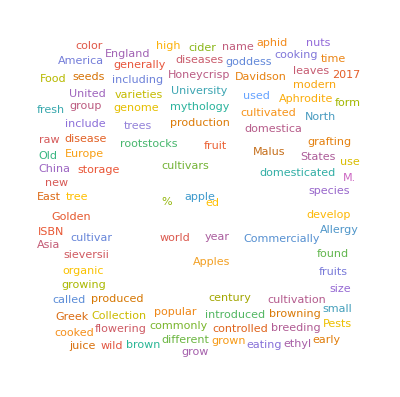
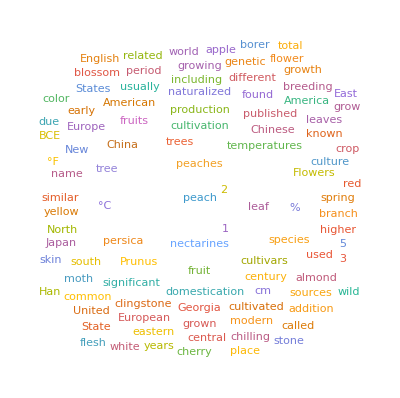
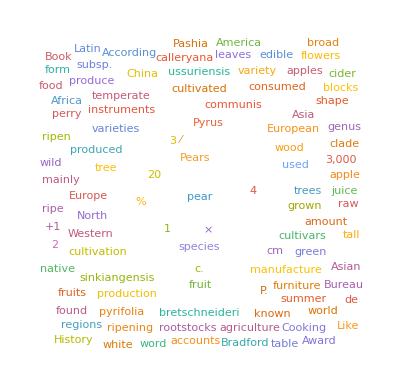

```mathematica
WordCloud[WikipediaData[#]]&/@{"apple","peach","pear"}
```

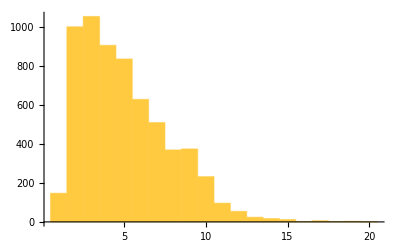
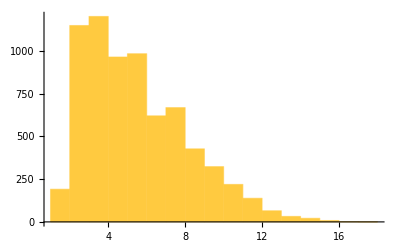
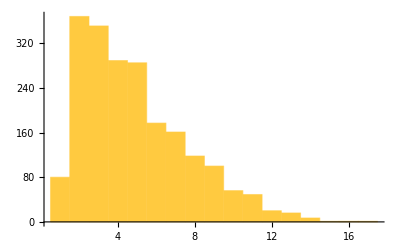

```mathematica
Histogram[StringLength[TextWords[WikipediaData[#]]]]&/@{"apple","peach","pear"}
```

```mathematica
GeoListPlot[#,GeoRange->]&/@EntityList[]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}